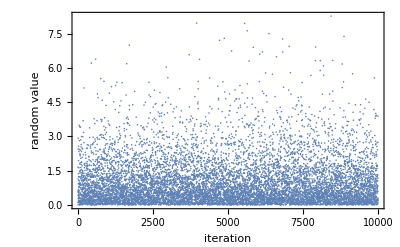

```mathematica
n=10000;
rlist=Table[-Log[Random[]],{i,1,n}];
Show[ListPlot[rlist,Frame->True,FrameLabel->{"iteration","random value"}],PlotRange->All]
(* If we take the logarithm of random numbers, we get a distribution that doesn't look uniform.  It's also not bounded by 1.  What is the distribution? *)
```

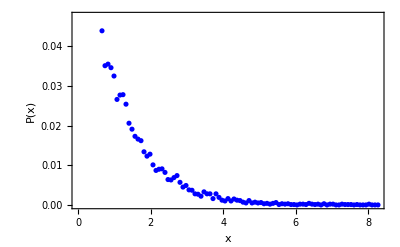

```mathematica
nbin=100;
bins=Table[{i Max[rlist]/100,0},{i,1,nbin}];
Do[
rval=rlist[[i]];  (*pick a random value to bin *)
Do[
If[rval<bins[[j,1]],  (* if that random value is smaller than the current bin,*)
bins[[j,2]]+=1./n;  (* put it into the bin *)
Break[] (* once we found its bin, stop! *)
];
,{j,1,nbin}];  (* search over all bins *)

,{i,1,n}]; (* check all numbers *)
p1=ListPlot[bins,PlotStyle->Blue,Frame->True,Axes->False,FrameLabel->{"x","P(x)"}]  (* plot the data *)


(* this is definitely not a uniform distribution.  It's decreasing.  *)
```

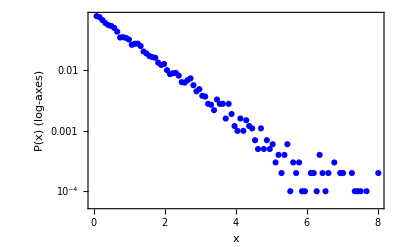

```mathematica
logplot=ListLogPlot[bins,PlotStyle->Blue,Frame->True,FrameLabel->{"x","P(x) (log-axes)"}] (*switching to logarithmic y-axes shows a roughly linear decrease.  If that were true, this would have an exponential decrease (log[y] being linear).  *)
```

{A→0.0868959,B→1.01167}

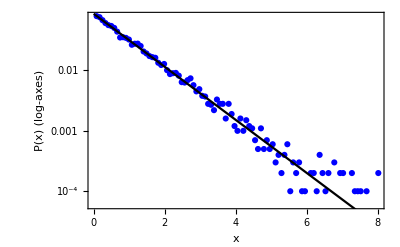

KS-test had statistic:  {0.385464,Do not reject}

```mathematica
bestFit=FindFit[bins,A Exp[-B x],{A,B},x]  (* lets find parameters that fit this data *)
fitplot=LogPlot[A Exp[-B x]/.bestFit,{x,0,10},PlotStyle->Black];
Show[logplot,fitplot,Frame->True,FrameLabel->{"x","P(x) (log-axes)"}]
(* this is a pretty reasonable fit, but not entirely convincing... *)
Print["KS-test had statistic:  ",KolmogorovSmirnovTest[rlist,ExponentialDistribution[B/.bestFit],{"PValue","ShortTestConclusion"}]]
```